## B80 Data Set

```mathematica
data80=Import["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/plots_skype_dec5th_2017/Data/current_with_prior/B80-mean-current-prior.txt","Table"];
Data80=Table[{data80[[i,1]]*1000,data80[[i,2]]*10^-5},{i,1,Length[data80]}];
vdfInt80=Interpolation[Data80];

data80UP=Import["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/plots_skype_dec5th_2017/Data/current_with_prior/B80-upper-current-prior.txt","Table"];
Data80UP=Table[{data80UP[[i,1]]*1000,data80UP[[i,2]]*10^-5},{i,1,Length[data80UP]}];
vdfInt80UP=Interpolation[Data80UP];

data80LO=Import["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/plots_skype_dec5th_2017/Data/current_with_prior/B80-lower-current-prior.txt","Table"];
Data80LO=Table[{data80LO[[i,1]]*1000,data80LO[[i,2]]*10^-5},{i,1,Length[data80LO]}];
vdfInt80LO=Interpolation[Data80LO];


PR80={{0,550},{0.0,0.5}};
P80=Plot[vdfInt80[x*1000]*10^5,{x,0,Data80[[Length[Data80],1]]/1000},PlotRange->PR80,PlotStyle-> {Blue,Thickness[0.003]},AspectRatio->1.0,FrameLabel->{{"f_v (100 km s^-1)",None},{"v (km s^-1)","Bhattacharjee et.al. (8.0, 200)"}},LabelStyle->{FontFamily->"Iowan Old Style",FontSize->35,Black},ImageSize->1200,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->False,ImagePadding->125,Epilog->{{RGBColor[0,0,1,1],Thickness[0.002],Line[{{350,0.45},{450,0.45}}]},{RGBColor[0,0,0,1],Thickness[0.002],Dashing[0.02],Line[{{350,0.4},{450,0.4}}]},RGBColor[0,0,0,1],Thickness[0.002],Dashing[0.04],Line[{{350,0.35},{450,0.35}}],{RGBColor[0,0,0,1],Thickness[0.002],Dotted,Line[{{50,0.45},{125,0.45}}]},{RGBColor[1,0,0,1],Thickness[0.002],Dotted,Line[{{50,0.4},{125,0.4}}]},Text[Style["The VDF",FontFamily->"Iowan Old Style",25,Blue],{500,0.45}],Text[Style["Bhatt. Fit",FontFamily->"Iowan Old Style",25,Black],{500,0.4}],Text[Style["New Fit",FontFamily->"Iowan Old Style",25,Black],{500,0.35}],Text[Style["SHM",FontFamily->"Iowan Old Style",25,Black],{165,0.45}],Text[Style["Maxwell",FontFamily->"Iowan Old Style",25,Black],{165,0.4}]}];
```

## B85 Data Set

```mathematica
data85=Import["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/plots_skype_dec5th_2017/Data/current_with_prior/B85-mean-current-prior.txt","Table"];
Data85=Table[{data85[[i,1]]*1000,data85[[i,2]]*10^-5},{i,1,Length[data85]}];
vdfInt85=Interpolation[Data85];

data85UP=Import["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/plots_skype_dec5th_2017/Data/current_with_prior/B85-upper-current-prior.txt","Table"];
Data85UP=Table[{data85UP[[i,1]]*1000,data85UP[[i,2]]*10^-5},{i,1,Length[data85UP]}];
vdfInt85UP=Interpolation[Data85UP];

data85LO=Import["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/plots_skype_dec5th_2017/Data/current_with_prior/B85-lower-current-prior.txt","Table"];
Data85LO=Table[{data85LO[[i,1]]*1000,data85LO[[i,2]]*10^-5},{i,1,Length[data85LO]}];
vdfInt85LO=Interpolation[Data85LO];


PR85={{0,600},{0.0,0.5}};
P85=Plot[vdfInt85[x*1000]*10^5,{x,0,Data85[[Length[Data85],1]]/1000},PlotRange->PR85,PlotStyle-> {RGBColor[1,0,0,1],Thickness[0.003]},AspectRatio->0.75,FrameLabel->{{"4πv^2f(v) (100 km/s)^-1",None},{"v (km s^-1)",None}},LabelStyle->{FontFamily->"Iowan Old Style",FontSize->45,Black},ImageSize->1200,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->False,ImagePadding->150,Epilog->{{RGBColor[1,0,0,1],Thickness[0.002],Line[{{330,0.42},{400,0.42}}]},{RGBColor[0,0,0,1],Thickness[0.002],Dashing[0.02],Line[{{330,0.32},{400,0.32}}]},{RGBColor[0,0,0,1],Thickness[0.005],Dashing[0.04],Line[{{330,0.37},{400,0.37}}]},{RGBColor[0,0,0,1],Thickness[0.002],Dotted,Line[{{330,0.47},{400,0.47}}]},Text[Style["B220-8.5-67 (obs)",FontFamily->"Iowan Old Style",35,Black],{500,0.42}],Text[Style["Bhattacharjee et. al.",FontFamily->"Iowan Old Style",35,Black],{497,0.32}],Text[Style["Best Fit (Eq. 5)",FontFamily->"Iowan Old Style",35,Black],{480,0.37}],Text[Style["SHM",FontFamily->"Iowan Old Style",35,Black],{430,0.47}]}];

P85BOLD=Plot[vdfInt85[x*1000]*10^5,{x,0,Data85[[Length[Data85],1]]/1000},PlotRange->PR85,PlotStyle-> {RGBColor[1,0,0,1],Thickness[0.003]},AspectRatio->0.75,FrameLabel->{{"4πv^2f(v) (100 km/s)^-1",None},{"v (km s^-1)",None}},LabelStyle->{FontFamily->"Iowan Old Style",FontSize->45,Black},ImageSize->1200,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->False,ImagePadding->150,Epilog->{{RGBColor[1,0,0,1],Thickness[0.002],Line[{{330,0.42},{400,0.42}}]},{RGBColor[0,0,0,1],Thickness[0.002],Dashing[0.02],Line[{{330,0.32},{400,0.32}}]},{RGBColor[0,0,0,1],Thickness[0.005],Dashing[0.04],Line[{{330,0.37},{400,0.37}}]},{RGBColor[0,0,0,1],Thickness[0.002],Dotted,Line[{{330,0.47},{400,0.47}}]},Text[Style["B220-8.5-67 (obs)",FontFamily->"Iowan Old Style",35,Black],{500,0.42}],Text[Style["Bhattacharjee et. al.",FontFamily->"Iowan Old Style",35,Black],{497,0.32}],Text[Style["Best Fit (Eq. 5)",FontFamily->"Iowan Old Style",35,Black],{480,0.37}],Text[Style["SHM (iso)",FontFamily->"Iowan Old Style",35,Black],{457.5,0.47}]}];
```

## SHM - Fig. 1

```mathematica
dataSHM=Import["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/SHM-Curve.dat","Table"];
DataSHM=Table[{dataSHM[[i,1]],dataSHM[[i,2]]},{i,1,Length[dataSHM]}];
vdfSHM=Interpolation[DataSHM,InterpolationOrder->2];
Plot[vdfSHM[x],{x,0,600}];
```

## Trying To Fit the B80 Data

The Attempts

```mathematica
ASt=1.5*10^-16;
v0St=250000;
kSt=-1.4;
pSt=-1.5;



maxW80=NonlinearModelFit[Data80,A*y^2*Exp[-y^2/y0^2],{{A,10^-5},{y0,206000}},y];
FindFit[Data80, A*y^2*Exp[-y^2/y0^2],{{A,10^-5},{y0,206000}},y];


fvMModel80[y_]:=A*y^2((1+y^2/v0^2)^k Exp[-(y^2/v0^2)^(1-k)]-(1+(Data80[[Length[data80],1]])^2/v0^2)^k Exp[-((Data80[[Length[data80],1]])^2/v0^2)^(1-k)])
FitMod80=NonlinearModelFit[Data80,A*y^2((1+y^2/v0^2)^k Exp[-(y^2/v0^2)^(1-k)]-(1+(Data80[[Length[data80],1]])^2/v0^2)^k Exp[-((Data80[[Length[data80],1]])^2/v0^2)^(1-k)]),{{k,kSt},{A,ASt},{v0,v0St}},y];

FindFit[Data80,A*y^2((1+y^2/v0^2)^k Exp[-(y^2/v0^2)^(1-k)]-(1+(Data80[[Length[data80],1]])^2/v0^2)^k Exp[-((Data80[[Length[data80],1]])^2/v0^2)^(1-k)]),{{k,kSt},{A,ASt},{v0,v0St}},y];


fvM2Model80[y_]:=A*y^2((1+y^2/v0^2)^k Exp[-(y^2/v0^2)^(1-p)]-(1+(Data80[[Length[data80],1]])^2/v0^2)^k Exp[-((Data80[[Length[data80],1]])^2/v0^2)^(1-p)])
Fit2Mod80=NonlinearModelFit[Data80,A*y^2((1+y^2/v0^2)^k Exp[-(y^2/v0^2)^(1-p)]-(1+(Data80[[Length[data80],1]])^2/v0^2)^k Exp[-((Data80[[Length[data80],1]])^2/v0^2)^(1-p)]),{{k,kSt},{p,pSt},{A,ASt},{v0,v0St}},y];
Fit2Mod80[{"CovarianceMatrix","ParameterErrors"}];

FindFit[Data80,A*y^2((1+y^2/v0^2)^k Exp[-(y^2/v0^2)^(1-p)]-(1+(Data80[[Length[data80],1]])^2/v0^2)^k Exp[-((Data80[[Length[data80],1]])^2/v0^2)^(1-p)]),{{k,kSt},{p,pSt},{A,ASt},{v0,v0St}},y]
FindFit[Data80UP,A*y^2((1+y^2/v0^2)^k Exp[-(y^2/v0^2)^(1-p)]-(1+(Data80UP[[Length[data80UP],1]])^2/v0^2)^k Exp[-((Data80UP[[Length[data80UP],1]])^2/v0^2)^(1-p)]),{{k,kSt},{p,pSt},{A,ASt},{v0,v0St}},y]
FindFit[Data80LO,A*y^2((1+y^2/v0^2)^k Exp[-(y^2/v0^2)^(1-p)]-(1+(Data80LO[[Length[data80LO],1]])^2/v0^2)^k Exp[-((Data80LO[[Length[data80LO],1]])^2/v0^2)^(1-p)]),{{k,kSt},{p,pSt},{A,ASt},{v0,v0St}},y]
```

{k→0.439983,p→-0.45473,A→1.22818×10^-16,v0→262996.}

{k→-0.219451,p→-0.255983,A→1.85144×10^-16,v0→275861.}

{k→0.520668,p→-0.989701,A→7.94563×10^-17,v0→288294.}

Checking the Fits

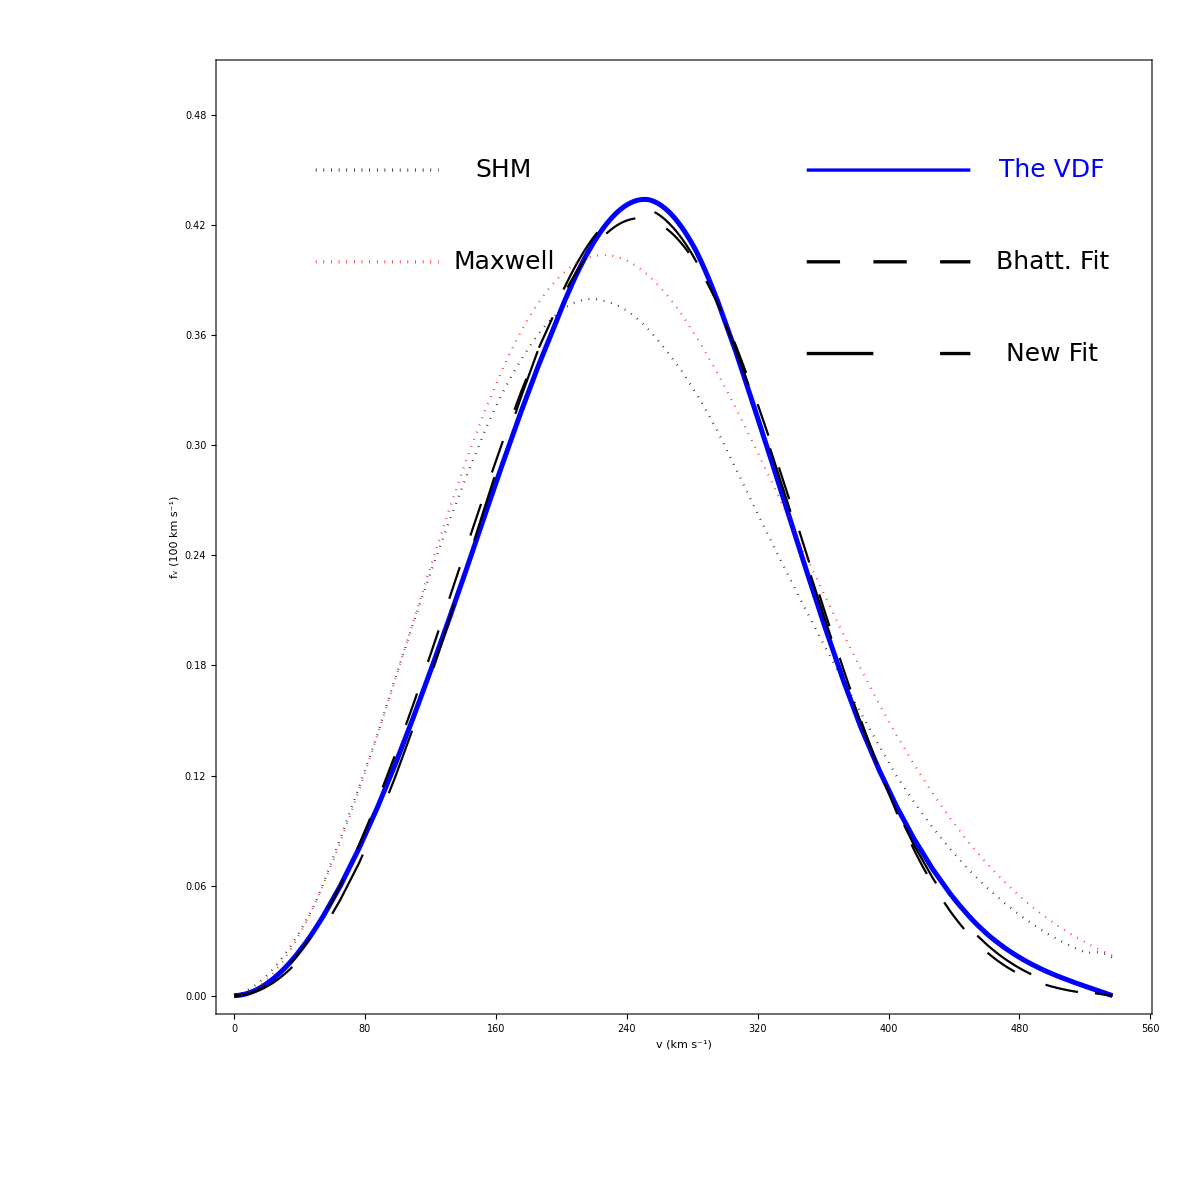

ItemAspectRatio::shdw: Symbol "ItemAspectRatio" appears in multiple contexts {"System`", "Global`"}; definitions in context "System`" may shadow or be shadowed by other definitions.

```mathematica
PFitCheck80=Plot[FitMod80[y*1000]*10^5,{y,0,Data80[[Length[data80],1]]/1000}, PlotStyle->{Dashing[0.02], Black}];

PFitCheck80New=Plot[Fit2Mod80[y*1000]*10^5,{y,0,Data80[[Length[data80],1]]/1000}, PlotStyle->{Dashing[0.04], Black}];

PFitMaxw80=Plot[10^5*maxW80[y*1000],{y,0,Data80[[Length[data80],1]]/1000},PlotStyle->{Dotted, Red}];

PSHM80=Plot[vdfSHM[y],{y,0,Data80[[Length[data80],1]]/1000},PlotStyle->{Dotted, Black}];

Show[P80,PFitCheck80,PFitCheck80New,PFitMaxw80,PSHM80]
Export["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/PFits80.png",Show[P80,PFitCheck80,PFitCheck80New,PFitMaxw80,PSHM80],"PNG"];
```

Percentage Errors

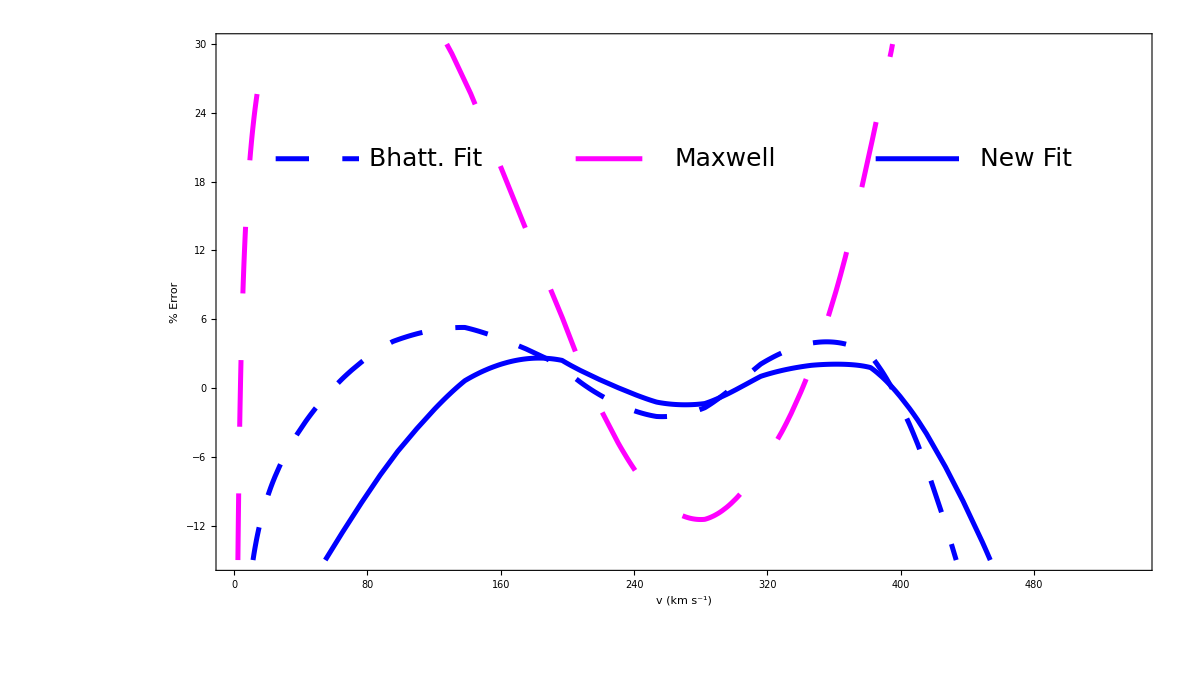

```mathematica
PR80E1={{0,540},{-10,10}};
PR80E2={{0,540},{-15,30}};

ErrBhatt80[x_]:=(FitMod80[x]-vdfInt80[x])/vdfInt80[x]*100
ErrNew80[x_]:=(Fit2Mod80[x]-vdfInt80[x])/vdfInt80[x]*100
ErrMax80[x_]:=(maxW80[x]-vdfInt80[x])/vdfInt80[x]*100



P80EBhatt=Plot[ErrBhatt80[x*1000],{x,0,Data80[[Length[Data80],1]]/1000},PlotRange->PR80E1,PlotStyle-> {Blue,Dashing[0.02],Thickness[0.003]},AspectRatio->9/16,FrameLabel->{{"% Error",None},{"v (km s^-1)","Bhattacharjee et.al. (8.0, 200)"}},LabelStyle->{FontFamily->"Iowan Old Style",FontSize->35,Black},ImageSize->1200,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->False,ImagePadding->125,Epilog->{{Blue,Dashing[0.02],Thickness[0.003],Line[{{50,7.5},{150,7.5}}]},Text[Style["Bhatt. Fit",FontFamily->"Iowan Old Style",25,Black],{200,7.5}],{Blue,Thickness[0.003],Line[{{350,7.5},{450,7.5}}]},Text[Style["New Fit",FontFamily->"Iowan Old Style",25,Black],{500,7.5}]}];
P80ENew=Plot[ErrNew80[x*1000],{x,0,Data80[[Length[Data80],1]]/1000},PlotRange->PR80E1,PlotStyle-> {Blue,Thickness[0.003]}];
Show[P80EBhatt,P80ENew];

Export["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/Err80.png",Show[P80EBhatt,P80ENew],"PNG"];



P80EBhatt2=Plot[ErrBhatt80[x*1000],{x,0,Data80[[Length[Data80],1]]/1000},PlotRange->PR80E2,PlotStyle-> {Blue,Dashing[0.02],Thickness[0.003]},AspectRatio->9/16,FrameLabel->{{"% Error",None},{"v (km s^-1)","Bhattacharjee et.al. (8.0, 200)"}},LabelStyle->{FontFamily->"Iowan Old Style",FontSize->35,Black},ImageSize->1200,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->False,ImagePadding->125,Epilog->{{Blue,Dashing[0.02],Thickness[0.003],Line[{{25,20},{75,20}}]},Text[Style["Bhatt. Fit",FontFamily->"Iowan Old Style",25,Black],{115,20}],{Magenta,Dashing[0.04],Thickness[0.003],Line[{{205,20},{255,20}}]},Text[Style["Maxwell",FontFamily->"Iowan Old Style",25,Black],{295,20}],{Blue,Thickness[0.003],Line[{{385,20},{435,20}}]},Text[Style["New Fit",FontFamily->"Iowan Old Style",25,Black],{475,20}]}];
P80ENew2=Plot[ErrNew80[x*1000],{x,0,Data80[[Length[Data80],1]]/1000},PlotRange->PR80E2,PlotStyle-> {Blue,Thickness[0.003]}];
P80EMax2=Plot[ErrMax80[x*1000],{x,0,Data80[[Length[Data80],1]]/1000},PlotRange->PR80E2,PlotStyle-> {Magenta,Thickness[0.003],Dashing[0.04]}];
Show[P80EBhatt2,P80ENew2,P80EMax2]

Export["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/Err80(2).png",Show[P80EBhatt2,P80ENew2,P80EMax2],"PNG"];
```

## Trying To Fit the B85 Data

The Attempts

```mathematica
ASt=1.5*10^-16;
v0St=350000;
kSt=-1.4;

ASt2=1.5*10^-10;
v0St2=250000;
kSt2=1.3;
pSt=-1.5;


maxW85=NonlinearModelFit[Data85,A*y^2*Exp[-y^2/y0^2],{{A,10^-5},{y0,206000}},y];
FindFit[Data85, A*y^2*Exp[-y^2/y0^2],{{A,10^-5},{y0,206000}},y];


fvMModel85[y_]:=A*y^2((1+y^2/v0^2)^k Exp[-(y^2/v0^2)^(1-k)]-(1+(Data85[[Length[data85],1]])^2/v0^2)^k Exp[-((Data85[[Length[data85],1]])^2/v0^2)^(1-k)])
FitMod85=NonlinearModelFit[Data85,A*y^2((1+y^2/v0^2)^k Exp[-(y^2/v0^2)^(1-k)]-(1+(Data85[[Length[data85],1]])^2/v0^2)^k Exp[-((Data85[[Length[data85],1]])^2/v0^2)^(1-k)]),{{k,kSt},{A,ASt},{v0,v0St}},y];

FindFit[Data85,A*y^2((1+y^2/v0^2)^k Exp[-(y^2/v0^2)^(1-k)]-(1+(Data85[[Length[data85],1]])^2/v0^2)^k Exp[-((Data85[[Length[data85],1]])^2/v0^2)^(1-k)]),{{k,kSt},{A,ASt},{v0,v0St}},y];


fvM2Model85[y_]:=A*y^2((1+y^2/v0^2)^k Exp[-(y^2/v0^2)^(1-p)]-(1+(Data85[[Length[data85],1]])^2/v0^2)^k Exp[-((Data85[[Length[data85],1]])^2/v0^2)^(1-p)])
Fit2Mod85=NonlinearModelFit[Data85,A*y^2((1+y^2/v0^2)^k Exp[-(y^2/v0^2)^(1-p)]-(1+(Data85[[Length[data85],1]])^2/v0^2)^k Exp[-((Data85[[Length[data85],1]])^2/v0^2)^(1-p)]),{{k,kSt},{p,pSt},{A,ASt},{v0,v0St}},y];
Fit2Mod85[{"CovarianceMatrix","ParameterErrors"}];

FindFit[Data85,A*y^2((1+y^2/v0^2)^k Exp[-(y^2/v0^2)^(1-p)]-(1+(Data85[[Length[data85],1]])^2/v0^2)^k Exp[-((Data85[[Length[data85],1]])^2/v0^2)^(1-p)]),{{k,kSt},{p,pSt},{A,ASt},{v0,v0St}},y]
FindFit[Data85UP,A*y^2((1+y^2/v0^2)^k Exp[-(y^2/v0^2)^(1-p)]-(1+(Data85UP[[Length[data85UP],1]])^2/v0^2)^k Exp[-((Data85UP[[Length[data85UP],1]])^2/v0^2)^(1-p)]),{{k,kSt},{p,pSt},{A,ASt},{v0,v0St}},y]
FindFit[Data85LO,A*y^2((1+y^2/v0^2)^k Exp[-(y^2/v0^2)^(1-p)]-(1+(Data85LO[[Length[data85LO],1]])^2/v0^2)^k Exp[-((Data85LO[[Length[data85LO],1]])^2/v0^2)^(1-p)]),{{k,kSt},{p,pSt},{A,ASt},{v0,v0St}},y]
```

{k→-2.48059,p→-1.68668,A→1.8926×10^-16,v0→372251.}

{k→-4.89988,p→-4.25483,A→2.54124×10^-16,v0→455026.}

{k→-0.991074,p→-1.83658,A→1.14892×10^-16,v0→332318.}

Checking the Fits

```mathematica
PFitCheck85=Plot[FitMod85[y*1000]*10^5,{y,0,Data85[[Length[data85],1]]/1000}, PlotStyle->{Dashing[0.02], Black}];

PFitCheck85New=Plot[Fit2Mod85[y*1000]*10^5,{y,0,Data85[[Length[data85],1]]/1000}, PlotStyle->{Dashing[0.04], Thickness[0.005],Black}];

PFitMaxw85=Plot[10^5*maxW85[y*1000],{y,0,Data85[[Length[data85],1]]/1000},PlotStyle->{Dotted, Black}];

PSHM = ListCurvePathPlot[DataSHM,PlotStyle->{Dotted, Black,Thickness[0.002]},InterpolationOrder->2];

Show[P85,PFitCheck85,PFitCheck85New,PFitMaxw85];
Export["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/PFits85.png",Show[P85,PFitCheck85,PFitCheck85New,PFitMaxw85],"PNG"];

Show[P85BOLD,PFitCheck85,PFitCheck85New,PFitMaxw85];
Export["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/PFits85BOLD.png",Show[P85BOLD,PFitCheck85,PFitCheck85New,PFitMaxw85],"PNG"];



Show[P85,PFitCheck85,PFitCheck85New,PSHM];
Export["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/PFits8530May.png",Show[P85,PFitCheck85,PFitCheck85New,PSHM80],"PNG"];

Show[P85BOLD,PFitCheck85,PFitCheck85New,PSHM]
Export["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/PFits85BOLD30May.png",Show[P85BOLD,PFitCheck85,PFitCheck85New,PSHM80],"PNG"];
Export["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/PFits85BOLD30May.pdf",Show[P85BOLD,PFitCheck85,PFitCheck85New,PSHM80],"PDF"];
Export["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/PFits85BOLD30May.eps",Show[P85BOLD,PFitCheck85,PFitCheck85New,PSHM80],"EPS"];
```

-Graphics-

Percentage Errors

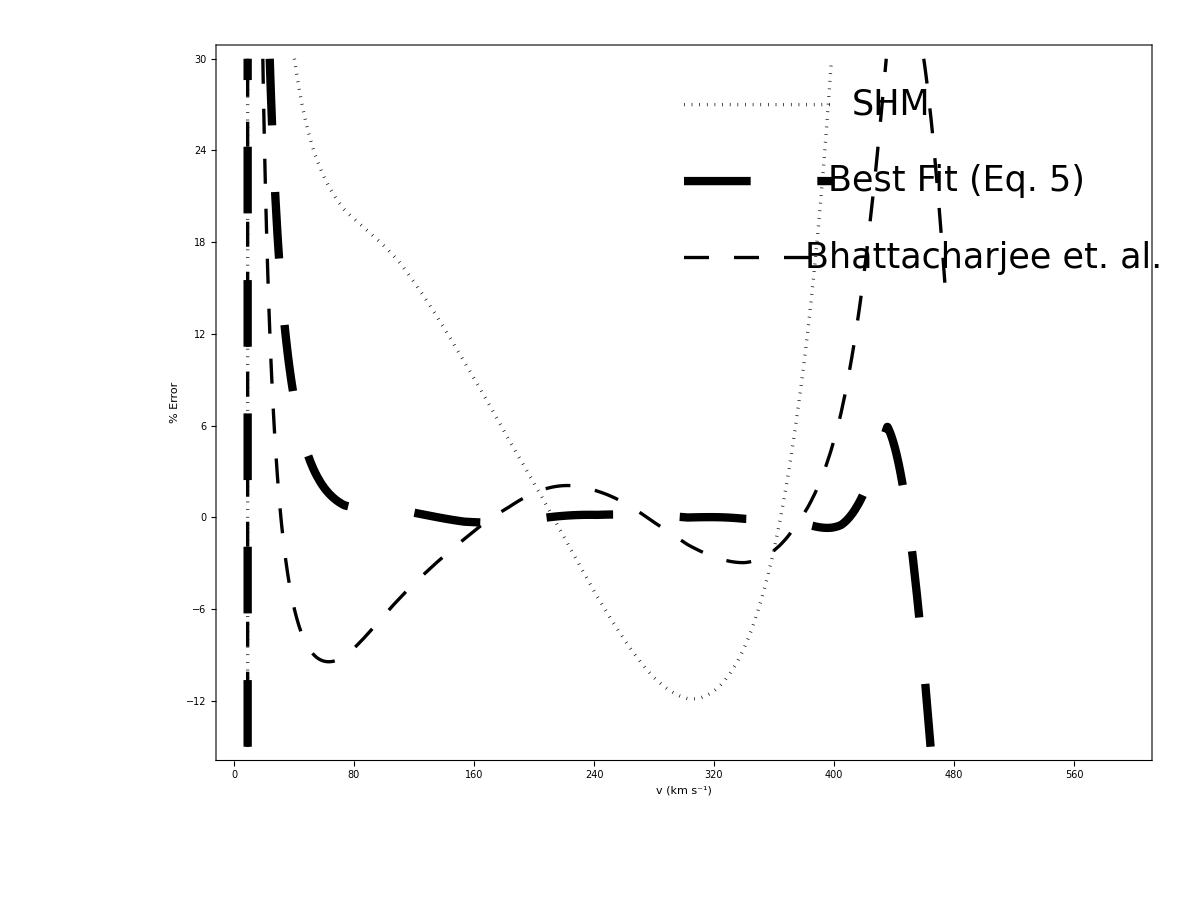

```mathematica
PR85E1={{0,600},{-10,10}};
PR85E2={{0,600},{-15,30}};

ErrBhatt85[x_]:=(FitMod85[x]-vdfInt85[x])/vdfInt85[x]*100
ErrNew85[x_]:=(Fit2Mod85[x]-vdfInt85[x])/vdfInt85[x]*100
ErrMax85[x_]:=(maxW85[x]-vdfInt85[x])/vdfInt85[x]*100


P85EBhatt=Plot[ErrBhatt85[x*1000],{x,0,Data85[[Length[Data85],1]]/1000},PlotRange->PR85E1,PlotStyle-> {Red,Dashing[0.02],Thickness[0.003]},AspectRatio->9/16,FrameLabel->{{"% Error",None},{"v (km s^-1)","Bhattacharjee et.al. (8.5, 220)"}},LabelStyle->{FontFamily->"Iowan Old Style",FontSize->35,Black},ImageSize->1200,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->False,ImagePadding->125,Epilog->{{Red,Dashing[0.02],Thickness[0.003],Line[{{50,7.5},{150,7.5}}]},Text[Style["Bhatt. Fit",FontFamily->"Iowan Old Style",25,Black],{200,7.5}],{Red,Thickness[0.003],Line[{{350,7.5},{450,7.5}}]},Text[Style["New Fit",FontFamily->"Iowan Old Style",25,Black],{500,7.5}]}];
P85ENew=Plot[ErrNew85[x*1000],{x,0,Data85[[Length[Data85],1]]/1000},PlotRange->PR85E1,PlotStyle-> {Red,Thickness[0.003]}];
Show[P85EBhatt,P85ENew];

Export["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/Err85.png",Show[P85EBhatt,P85ENew],"PNG"];


P85EBhatt2=Plot[ErrBhatt85[x*1000],{x,0,Data85[[Length[Data85],1]]/1000},PlotRange->PR85E2,PlotStyle->{Dashing[0.015],Thickness[0.002], Black},AspectRatio->0.75,FrameLabel->{{"% Error",None},{"v (km s^-1)",None}},LabelStyle->{FontFamily->"Iowan Old Style",FontSize->45,Black},ImageSize->1200,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->False,ImagePadding->150,Epilog->{{Dashing[0.015],Thickness[0.002], Black,Line[{{300,17},{400,17}}]},Text[Style["Bhattacharjee et. al.",FontFamily->"Iowan Old Style",35,Black],{500,17}],{Dotted,Thickness[0.002],Black,Line[{{300,27},{400,27}}]},Text[Style["SHM",FontFamily->"Iowan Old Style",35,Black],{438,27}],{Dashing[0.04], Thickness[0.005],Black,Line[{{300,22},{400,22}}]},Text[Style["Best Fit (Eq. 5)",FontFamily->"Iowan Old Style",35,Black],{482,22}]}];
P85ENew2=Plot[ErrNew85[x*1000],{x,0,Data85[[Length[Data85],1]]/1000},PlotRange->PR85E2,PlotStyle->{Dashing[0.04], Thickness[0.005],Black}];
P85EMax2=Plot[ErrMax85[x*1000],{x,0,Data85[[Length[Data85],1]]/1000},PlotRange->PR85E2,PlotStyle->{Dotted,Thickness[0.002],Black}];
Show[P85EBhatt2,P85ENew2,P85EMax2]

Export["/Users/sayan/Dropbox/direct_detection_velocity_profiles/nov_30th_2017/Err85(2).png",Show[P85EBhatt2,P85ENew2,P85EMax2],"PNG"];
```